# Feeding on n-prey-at-a-time

## Preamble

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
SetDirectory["../../figs/"]
```

/Users/novakm/Git/FR_n-prey-at-a-time/code/mathematica

/Users/novakm/Git/FR_n-prey-at-a-time/figs

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

## Functional response

#### Partial summation

```mathematica
Sum[x^i,{i,0,n}]
s=Sum[x^i,{i,1,n}]
(s/(1+s))//Simplify
```

(-1+x^(1+n))/(-1+x)

(x (-1+x^n))/(-1+x)

(x (-1+x^n))/(-1+x^(1+n))

#### Infinite summation

```mathematica
Sum[x^i,{i,0,∞}]
s=Sum[x^i,{i,1,∞}]
(s/(1+s))//Simplify
```

1/(1-x)

-x/(-1+x)

x

### Feeding on n prey at a time - Functional response

Now  substitute  ' x -> a h R' to get ...

```mathematica
S[n_]=Sum[(a h R )^i,{i,1,n}];
fracF[n_,R_]=(S[n]/(1+S[n]))//Simplify
f[n_,R_]=(1/h)fracF[n,R]
```

(a h R (-1+(a h R)^n))/(-1+(a h R)^(1+n))

(a R (-1+(a h R)^n))/(-1+(a h R)^(1+n))

```mathematica
f[1,R]//Simplify
f[2,R]
%//Simplify
f[3,R]
f[4,R]
f[0.5,R]
f[1.5,R]
```

(a R)/(1+a h R)

(a R (-1+a^2 h^2 R^2))/(-1+a^3 h^3 R^3)

(a R (1+a h R))/(1+a h R+a^2 h^2 R^2)

(a R (-1+a^3 h^3 R^3))/(-1+a^4 h^4 R^4)

(a R (-1+a^4 h^4 R^4))/(-1+a^5 h^5 R^5)

(a R (-1+(a h R)^0.5))/(-1+(a h R)^1.5)

(a R (-1+(a h R)^1.5))/(-1+(a h R)^2.5)

### Fraction handling i prey

```mathematica
fracFn[i_,n_,R_]=((a h R)^i/(1+S[n]))//Simplify
```

((a h R)^i (-1+a h R))/(-1+(a h R)^(1+n))

```mathematica
fracFn[1,2,R]//Simplify
```

(a h R)/(1+a h R+a^2 h^2 R^2)

#### Infinite summation gives the “Type 1” functional response

```mathematica
Sinf[n_]=Sum[(a h R)^i,{i,1,∞}];
finf[R_]=(1/h)(Sinf[n]/(1+Sinf[n]));
finf[R]//Simplify
```

a R

### Illustrate multiple-prey functional response

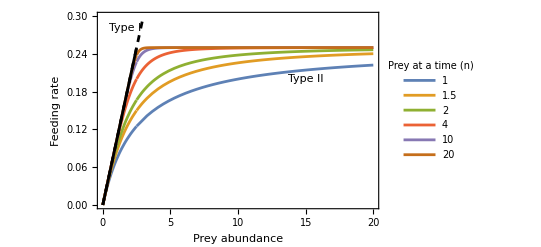

```mathematica
Clear[fparms]
Clear[nvals]
fparms={h-> 4,a-> 0.1};
nvals={1,1.5,2, 4, 10, 20};

prange = {{0,20},{0,0.3}};
p1=Plot[Evaluate[f[n,R]/.fparms/.n-> nvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[nvals,
LegendLabel-> "Prey at a time (n)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]},
Epilog-> Text["Type II",{15,0.2}]
];
p2a=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black,Dashed},
PlotLabels-> Placed[{"Type I"},{1.7,0.27},Background-> None]];
p2b=Plot[finf[R]/.fparms,{R,0,1/(a h)/.fparms},
PlotRange->prange,
PlotStyle->{Black}];
P1=Show[p1,p2a,p2b]
Export["FR_n-prey-at-a-time.pdf",P1,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Fraction of predator population handling exactly i of n-max prey

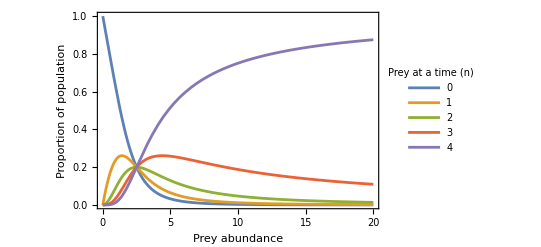

```mathematica
nmax=4;
prange = {{0,20},{0,1}};
P8=Plot[{1-fracF[nmax,R]/.fparms,Evaluate[Table[fracFn[i,nmax,R]/.fparms,{i,1,nmax}]]},{R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[Range[0,nmax],
LegendLabel-> "Prey at a time (n)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Center}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Proportion of population",14]}]
Export["FR_n-prey-at-a-time_fracF.pdf",P8,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

Prey abundance where predator proportions are all equal

```mathematica
Solve[fracFn[1,nmax,R]==fracFn[2,nmax,R],R]
```

{{R→0},{R→1/(a h)}}

### Compare to diminishing handling times

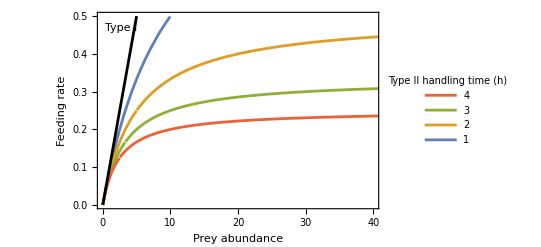

```mathematica
hvals = Table[h,{h,1,4,1}];

prange = {{0,40},{0,0.5}};
p3=Plot[Evaluate[f[1,R]/.Drop[fparms,1]/.h-> hvals], {R,0,100},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[hvals,
LegendLabel-> "Type II handling time (h)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"ReversedRow",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]}
];
p2=Plot[finf[R]/.fparms,{R,0,100},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},{2.8,0.45},Background-> None]];
P2=Show[p3,p2]
Export["FR_htime-to-zero.pdf",P2,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Density-dependent diminishing handling time (exponential decay)

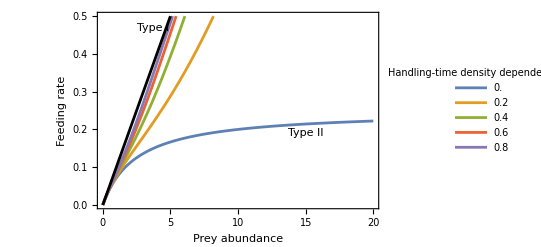

```mathematica
fT2h[R_]=(a R)/(1 + a h Exp[-(η R)] R);
ηvals = Table[η,{η,0,0.8,0.2}];

prange = {{0,20},{0,0.5}};
p4=Plot[Evaluate[fT2h[R]/.fparms/.η->ηvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[ηvals,
LegendLabel-> "Handling-time density dependence (η)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]},
Epilog-> Text["Type II",{15,0.19}]
];
p2=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},{{2.5,0.45},{0,0}}],Background->Transparent];
P3=Show[p4,p2]
Export["FR_htime_diminishing.pdf",P3,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Density-dependent diminishing handling time (adaptively-optimal prey; Okuyama 2010)

```mathematica
fT2h2[R_]=(a R)/(1 + a (√(a R Θ))/(a R) R)//Simplify;
Θvals = Table[Θ,{Θ,2,8,2}];
```

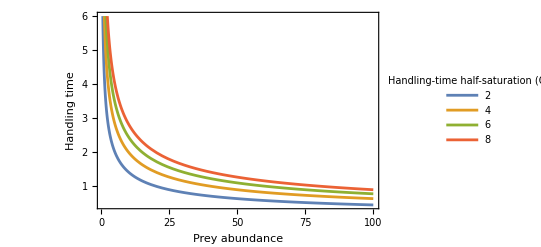

```mathematica
Plot[Evaluate[Table[(√(a R Θ))/(a R)/.fparms,{Θ,2,8,2}]], {R,0,100},
PlotRange->{{0,All},{0,6}},
PlotLegends -> Placed[
LineLegend[Θvals,
LegendLabel-> "Handling-time half-saturation (Θ)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Top}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Handling time",14]}]
```

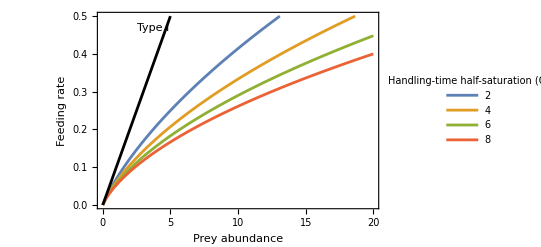

```mathematica
prange = {{0,20},{0,0.5}};
p4b=Plot[Evaluate[fT2h2[R]/.fparms/.Θ->Θvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[Θvals,
LegendLabel-> "Handling-time half-saturation (Θ)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]}
];
p2b=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},{{2.5,0.45},{0,0}}],Background->Transparent];
P3b=Show[p4b,p2b]
Export["FR_htime_diminishing-opt.pdf",P3b,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

## Modify Rosenzweig-MacArthur model

```mathematica
Clear[nvals]
nvals={1,2, 4, 10, 20};

(*Good isocline spacing over dynamical range*)
(* parms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2} *)
parms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2};
```

```mathematica
dRdt=r R (1-R/Κ)-f[n,R]P;
dPdt=e f[n,R]P-d P;

modelC[n_]:={
R'[t]==r R[t](1-R[t]/Κ)-f[n,R]P[t],
R[0]==0.1,
P'[t]==e f[n,R[t]]P[t]-d P[t],
P[0]==0.1
};
```

## Nullclines

#### Prey isocline

```mathematica
isoR[R_]=P/.Solve[dRdt==0,P]//FullSimplify
```

{(r (-1+(a h R)^(1+n)) (-R+Κ))/(a (-1+(a h R)^n) Κ)}

Slope at origin

```mathematica
isoRorig=Simplify[D[isoR[R],R]/.R-> 0, n>1]
```

{-r/(a Κ)}

Intercept  at  origin

```mathematica
isoRint=isoR[R]/.{R-> 0,n-> 1}
```

{r/a}

Compare to Type I and Type II

```mathematica
P/.Solve[(dRdt/.{h-> 0, n-> 1})==0,P]//FullSimplify
P/.Solve[(dRdt/.{h-> h, n-> 1})==0,P]//FullSimplify
```

{(r (-R+Κ))/(a Κ)}

{-(r (1+a h R) (R-Κ))/(a Κ)}

For  very  large  n, the prey isocline will converge to having the slope at origin extend to N=1/ah.  
Above N=1/ah the shape of the isocline will converge to that expected when the functional response is density independent (i.e. f(N) = 1/h).

```mathematica
isoRn[R_]=P/.Solve[r R (1-R/Κ)-1/h P==0,P]//FullSimplify
```

{(h r R (-R+Κ))/Κ}

#### Predator isocline

Type I and Type II

```mathematica
R/.Solve[(dPdt/.h-> 0)==0,R]//TableForm
R/.Solve[(dPdt/.{h-> 0,n-> 1})==0,R]//TableForm

R/.Solve[(dPdt/.n->1)==0,R]//TableForm
```

((-1+0^(1+n)) d)/((-1+0^n) a e)

d/(a e)

d/(a (e-d h))

#### Visualize

```mathematica
Clear[isoP]
isoP[ν_]:=Re[Select[R/.Solve[(dPdt/.n->ν)==0,R]/.parms,Abs[Im[#]]< 10^-13&&Re[#]>0&]]//Flatten
```

Values of predator isocline converge on constant very quickly

```mathematica
isoPvals=isoP/@nvals//Flatten
```

{44.4444,23.1,17.5223,16.0697,16.0008}

```mathematica
addEpilog[g_Graphics,epi_List]:=With[{styles=Cases[g[[1]],{dir__,__Line}:>Directive[dir],-5]},Show[g,Epilog->{styles,epi}~Flatten~{2}]]

p4=Plot[Evaluate[isoR[R]/.parms/.n-> nvals],{R,0,100},
PlotRange->{{0,1+Κ/.parms},{0,50}},
PlotRangePadding->0,
AspectRatio->0.8,
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey abundance",14],
Style["Predator abundance",14]}
];

p5a=Legended[
addEpilog[p4,InfiniteLine[{{#,0},{#,1}}]&/@isoPvals],
Placed[
LineLegend[
ColorData[97,"ColorList"][[1;;Length[nvals]]],
nvals,
LegendLabel-> "Prey at a time (n)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings-> 0.1],
{{0.7,0.57},{0,0}}]];
```

```mathematica
isoRvals=MapThread[ReplaceAll,{isoR[isoPvals]/.parms//Flatten,Thread[n->#]&/@nvals}];
pts=Transpose[{isoPvals,isoRvals}];
p5d=Graphics[Prepend[Riffle[ColorData[97,"ColorList"][[1;;Length[nvals]]],Point/@pts],PointSize[.02]]];
```

#### Add Isocline for linear Type I

```mathematica
dRdtinf=r R (1-R/Κ)-a R P;
dPdtinf=e a R P-d P;
isoRinf[R_]=P/.Solve[dRdtinf==0,P]
isoPinf=R/.Solve[dPdtinf==0,R]
```

{-(r (R-Κ))/(a Κ)}

{d/(a e)}

As n -> ∞ the many - prey prey isocline breaks away from the type - I prey isocline at R = 1/ (a h) . 
   [Obtained by solving ' a R = 1 / h' for R .]

```mathematica
p5b=Plot[Evaluate[isoRinf[R]/.parms],{R,0,100},
PlotLabels->Placed[{"Type I","Type II"},{{60,9},{90,16}},Background->Transparent],
PlotStyle->{Black,Dashed},
GridLines->{isoPinf/.parms,None},
GridLinesStyle->Directive[Thickness[0.003],Black]];
p5c=Plot[Evaluate[isoRinf[R]/.parms],{R,0,1/(a h)/.parms},
PlotStyle->Black];
```

Prey  isocline  converges  on ...  as  n  increases

```mathematica
p5e=Plot[isoRint+isoRorig R/.parms, {R, 0, 100},
PlotRange->{Full,Full},
PlotStyle->{Black,Dashed,Thickness[0.003]},
RegionFunction->Function[{x}, x < 1/(a h)/.parms]];
p5f=Plot[isoRn[R]/.parms, {R,1/(a h)/.parms, 100},
PlotStyle->{Black,Dashed,Thickness[0.003]}];
```

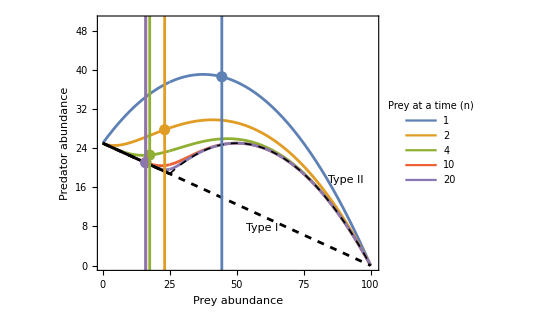

Isoclines.pdf

```mathematica
P4=Show[p5a,p5b,p5e,p5f,p5c,p5d]
Export["Isoclines.pdf",P4,"PDF",
"AllowRasterization"->False,ImageSize->360]
```

### Prey isocline as a function of handling time

```mathematica
hvals2={0.5,1,2,3,4};
```

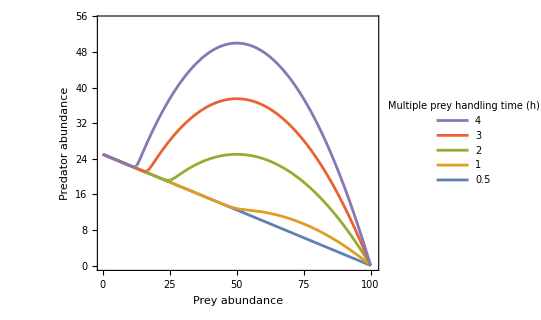

```mathematica
Plot[Evaluate[isoR[R]/.Drop[parms,-1]/.n-> 40/.h-> hvals2],{R,0,100},
PlotRange->{{0,1+Κ/.parms},{0,55}},
PlotRangePadding->0,
AspectRatio->0.8,
PlotLegends -> Placed[
LineLegend[hvals2,
LegendLabel-> "Multiple prey handling time (h)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"ReversedRow",1},
Spacings->0.15],
{Left,Bottom}],
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey abundance",14],
Style["Predator abundance",14]}]
```

#### Compare to Type II

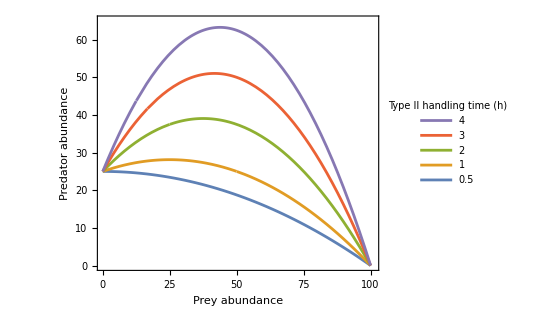

```mathematica
Plot[Evaluate[isoR[R]/.Drop[parms,-1]/.n-> 1/.h-> hvals2],{R,0,100},
PlotRange->{{0,1+Κ/.parms},{0,65}},
PlotRangePadding->0,
AspectRatio->0.8,
PlotLegends -> Placed[
LineLegend[hvals2,
LegendLabel-> "Type II handling time (h)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"ReversedRow",1},
Spacings->0.15],
{Left,Bottom}],
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey abundance",14],
Style["Predator abundance",14]}]
```

## Equilibria

```mathematica
A=JacobianMatrix[{dRdt,dPdt},{R,P}]//FullSimplify;
MatrixForm@A
```

Solving for equilbria symbolically for general ‘n’ is not possible , but solving for n < 3 works and results in ‘n’ potential  coexistence equilibria of which only one is feasible and real-valued.  It tends to be the 2nd equilibrium that is the feasible coexistence equilibrium.
Note that, when evaluated at the feasible coexistence steady state,  the [2, 2] element (predator effect on predator) of the Jacobian is always zero (regardless of n).  Thus the trace is determined entirely by the prey’s self-effect.
The [1,2] element (predator effect on prey) is always -d/e.

```mathematica
pickSS=2;
Clear[n]
```

#### n = 1

```mathematica
n=1;
equil=Solve[{dRdt==0,dPdt==0},{R,P}];
equil//TableForm
equil/.parms//TableForm

Aeq=A/.equil[[pickSS]]//Simplify;
MatrixForm@Aeq

Det[Aeq]//Simplify
Tr[Aeq]//Simplify

Det0=Solve[Det[Aeq]==0, d]
Tr0=Solve[Tr[Aeq]==0, d]
```

#### n = 2

```mathematica
n=2;
equil=Solve[{dRdt==0,dPdt==0},{R,P}];
equil//TableForm
equil/.parms//TableForm

Aeq=A/.equil[[pickSS]]//Simplify;
MatrixForm@Aeq

Det[Aeq]//Simplify
Tr[Aeq]//Simplify

Det0=Solve[Det[Aeq]==0, d]
(* Tr0=Solve[Tr[Aeq]==0, d] *)
```

#### n = 3

```mathematica
(* 


n=3;
equil=Solve[{dRdt==0,dPdt==0},{R,P}]//Simplify;
equil//TableForm
equil/.parms//TableForm

Aeq=A/.equil[[pickSS]]//Simplify;
MatrixForm@Aeq

Det[Aeq]//Simplify
Tr[Aeq]//Simplify

(* Det0=Solve[Det[Aeq]==0, d] *)
(* Tr0=Solve[Tr[Aeq]==0, d] *)


*)
```

## Exploration

```mathematica
Clear[n,smodelC];
A=JacobianMatrix[{dRdt,dPdt},{R,P}]//FullSimplify;

Manipulate[

smodelC[n_]:={
R'[t]==r R[t](1-R[t]/Κ)-(a R[t] (-1+(a h)^n (R[t])^n))/((a h)^(1+n) (R[t])^(1+n)-1)P[t],
R[0]==Rinit,
P'[t]==e (a R[t] (-1+(a h)^n (R[t])^n))/((a h)^(1+n) (R[t])^(1+n)-1)P[t]-d P[t],
P[0]==Pinit
};

subparms = {a-> α,r->ρ,e->ϵ,d->δ, Κ-> κ, h-> η};

sol=Quiet[First[NDSolve[{smodelC[ν]/.subparms},{R,P},{t,0,T},AccuracyGoal-> 2]]];

isoR[R_]=P/.Solve[dRdt==0,P];

(*isoP=R/.Quiet@Solve[(dPdt/.n->ν/.subparms)==0,R,Reals];*)
isoP=Re[Select[R/.Solve[(dPdt/.n->ν)==0,R]/.subparms,Abs[Im[#]]< 10^-13&&Re[#]>0&]]//Flatten;

equil=Select[NSolve[{dRdt==0,dPdt==0}/.subparms/.n-> ν,{R,P}],
Re[#[[1,2]]]>0&&Re[#[[2,2]]]>0 && Im[#[[1,2]]]==0&&Im[#[[2,2]]]==0&]//Flatten;

A=JacobianMatrix[{dRdt,dPdt},{R,P}]//FullSimplify;
Aeq=A/.equil/.subparms/.n-> ν;
{DetA,TrA}={Det[Aeq],Tr[Aeq]};

eig = Eigenvalues[Aeq];
dhe = (d h / e)/.subparms;

p1=Plot[Evaluate[{R[t],P[t]}/.sol],{t,0,T},
PlotRange->{0,All},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14],Style["Abundance",14]}];

p2=Plot[Evaluate[fracF[ν,R[t]/.sol]/.subparms],{t,0,T},
PlotRange-> {0,1},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14],Style["Fraction feeding",12]}];

p3=Plot[Evaluate[isoR[R]/.subparms/.n-> ν],{R,0,500},
PlotRange->{{0,1+Κ/.subparms},{0,70}},
PlotRangePadding->0,
AspectRatio->0.8,
GridLines-> {isoP,{-1,-1,-1}},
(*GridLines->{isoP/.subparms,None},*)
GridLinesStyle->Directive[Thickness[0.003],Orange],
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey",14],
Style["Predator",14]}];

p4=StreamPlot[{dRdt,dPdt}/.subparms/.n-> ν,{R,0,1+Κ/.subparms},{P,0,70}];
p5=ParametricPlot[Evaluate[{R[t],P[t]}/. sol,{t,0,T}],
ColorFunction->(ColorData["Rainbow"][#3]&)];

p6=Show[p3,p4,p5];

GraphicsGrid[{{p1,p2},{p3,p6}},ImageSize->Large],
{{Rinit,0.1,"R0"},0.1,100,0.1},
{{Pinit,0.1,"P0"},0.1,100,0.1},
{{ν,1,"n"},1,15,1},
{{α,0.02,"a"},0.001,0.1,0.001},
{{ρ,0.5,"r"},0.1,2,0.05},
{{ϵ,0.25,"e"},0.05,0.5,0.05},
{{δ,0.08,"d"},0.01,0.2,0.005},
{{κ,100,"K"},1,200,1},
{{η,2,"h"},0,5,0.05},
{{T,1000,"T"},1000,200000,1000},
Dynamic[Plot[f[ν,x]/.{a-> α, h-> η},{x,0,50},
PlotRange->Full,
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Resource abundance",10],Style["Feeding rate",10]}]],
Style["Steady state abundances",10,Bold],
Dynamic[equil],
Style["Eigenvalues",10,Bold],
Dynamic[eig],
Style["Determinant and Trace",10,Bold],
Dynamic[{DetA,TrA}],
Style["F",10,Bold],
Dynamic[dhe],
ControlPlacement->Left,
TrackedSymbols:>{ν,α,ρ,ϵ,δ,κ,η,T,Rinit,Pinit}
]
```

## Stability

Since equilibria can' t be solved for symbolically, proceed numerically.
Note that there are two feasible (real-valued) solutions at high n (as seen using Eigs2) due to the existence of two positive real predator isoclines (see above).

#### Eigenvalues as function of 'n'

```mathematica
MaxRe[λ_]:=Max[Re[λ]];
MaxIm[λ_]:=Max[Im[λ]]; 
(* imaginary parts are always equal magnitude (one positive on negative) so just take max *)
```

```mathematica
Eigs[ν_]:=
Module[{equil,A,Aeq},
equil=Select[NSolve[{dRdt==0,dPdt==0}/.parms/.n-> ν,{R,P}],
Re[#[[1,2]]]>0&&Re[#[[2,2]]]>0 && Im[#[[1,2]]]==0&&Im[#[[2,2]]]==0&]//Flatten;
A=JacobianMatrix[{dRdt,dPdt}/.parms/.n-> ν,{R,P}];
Aeq=A/.equil/.parms/.n-> ν;
Eigenvalues[Aeq]
]
Eigs2[ν_]:=
Module[{equil,A,Aeq,eigs,FeasRP},
equil=Quiet[NSolve[{dRdt==0,dPdt==0}/.parms/.n-> ν,{R,P}]];
FeasRP=Re[R]>0 && Re[P]> 0 && Im[R]==0 && Im[P]==0/.equil;
A=JacobianMatrix[{dRdt,dPdt}/.parms/.n-> ν,{R,P}];
Aeq=A/.Pick[equil,FeasRP];
Map[Eigenvalues,Aeq]]
```

Values at lower n than evaluated are unstable; the predator has gone extinct.

```mathematica
eigs0=Table[{n,Eigs[n]},{n,0.64,0.65,0.01}];
eigs1=Table[{n,Eigs[n]},{n,0.65,0.75,0.05}];
eigs2=Table[{n,Eigs[n]},{n,0.8,1.6,0.2}];
eigs3=Table[{n,Eigs[n]},{n,2,4,0.5}];
eigs4=Table[{n,Eigs[n]},{n,5,13,1}];
eigs=Join[eigs0,eigs1,eigs2,eigs3,eigs4];
```

```mathematica
eigRe=MapAt[MaxRe,eigs,{All,2}];
eigIm=MapAt[MaxIm,eigs,{All,2}];
```

```mathematica
ip={{50,50},{40,10}};
p6=ListPlot[
Callout[eigRe,"Re(λ_1)",{Scaled[0.6],Above},LeaderSize->0,Background->None],
Joined-> True,
ImagePadding->ip,
PlotRangePadding->{{0,0},{0.005,0.01}},
Axes->False,
GridLines->{{-10},{0}},
Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey at a time (n)",14],
Style["Re(λ_1)",14]}];
p7=ListPlot[
Callout[eigIm,"Im(λ_1)",{Scaled[0.6],Below},LeaderSize->0,Background->None],
Joined-> True,
ImagePadding->ip,
PlotRangePadding->{{0,0},{0,0}},
Axes->True,
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,True}},
PlotStyle-> Dashed,
FrameLabel->
{{None,Style["Im(λ_1)",14]},
{None,None}}];
P6=Overlay[{p7,p6}]

Export["Eigenvalues.pdf",P6,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Eigenvalues as function of ‘n’ and ‘K’

Need to restrict to integer values of  'n' to permit computation in reasonable time

```mathematica
nKparms = Drop[parms,{5}];

StableReImFeasRP[ν_,k_]:=
Module[{equil,A,Aeq,eigs,FeasRP,ReE,ImE},
equil=Quiet[Solve[{dRdt==0,dPdt==0}/.nKparms/.n-> ν/.Κ-> k,{R,P}]];
FeasRP=Re[R]>0 && Re[P]> 0 && Im[R]==0 && Im[P]==0/.equil;
A=JacobianMatrix[{dRdt,dPdt}/.nKparms/.n-> ν/.Κ-> k,{R,P}];
Aeq=A/.Pick[equil,FeasRP];
eigs=Map[Eigenvalues,Aeq];
WhichMaxRe=1;
ReE=Map[MaxRe,eigs][[WhichMaxRe]];
ImE=Map[MaxIm,eigs][[WhichMaxRe]];
If[!NumberQ[ReE],out=0,
If[ReE>=0,out=3,
If[ReE<0 && ImE==0,out=1,
If[ReE <0&&ImE>0,out=2]]]];
out
]
```

```mathematica
StableReImFeasRP[11,100]
```

```mathematica
nMax=13;
kMin=1;
kMax=250;
kStep=1;
stabReImRP=Table[StableReImFeasRP[n,κ],{κ,kMin,kMax,kStep},{n,1,nMax,1}];
```

```mathematica
xvals = Range[nMax];
yvals=Table[i,{i,0,kMax ,kStep}];
xticks=Transpose[{xvals,xvals}];
yticks=Transpose[{Range@Length[yvals] 10-10,yvals}];

P7=ArrayPlot[stabReImRP,
DataReversed->True,
ColorFunctionScaling->False,
ColorFunction->ColorData[{"GrayTones","Reverse"}],
ColorRules->{
x_/;x ==3 -> GrayLevel[0.4],
x_/;x ==2 -> GrayLevel[0.7],
x_/;x ==1 -> GrayLevel[0.9],
x_/;x ==0 -> GrayLevel[0.2]},
PlotRangePadding->None,
Frame->True,
FrameTicks->{{yticks,None},{xticks,None}},
AspectRatio->1,
FrameLabel->{
Style["Prey carrying capacity (K)",14],
Style["Prey at a time (n)",14]},
Epilog->{
Text[Style["Damped oscillations",14],{9,70}],
Text[Style["Monotonic damping",14],{8,23}],
Text[Style["Predator extinction",14, White],{6,8}],
Text[Style["Limit cycles",14, White],{3,180}]}]
```

```mathematica
smodelC2[ν_,k_]:={R'[t]==r R[t](1-R[t]/Κ)-(a R[t] (-1+(a h)^n (R[t])^n))/((a h)^(1+n) (R[t])^(1+n)-1)P[t],
P'[t]==e (a R[t] (-1+(a h)^n (R[t])^n))/((a h)^(1+n) (R[t])^(1+n)-1)P[t]-d P[t]}/.nKparms/.Κ-> k/.n-> ν;
```

```mathematica
OrbitTest[ν_,k_]:=
Module[{X,Y,pts,T,Tlag,Diff,Tol,Cnt},
T=150000;
Tlag=100;
Tol=10^-5;

{X,Y}=NDSolveValue[{smodelC2[ν,k],R[0]==0.05,P[0]==0.1},{R,P},{t,0,T},
AccuracyGoal->10,PrecisionGoal->10];

Diff=Abs[X[T]-X[T-Tlag]];
If[Diff<Tol,
pts={1},
pts=Reap[nd[{ν,k}]=Quiet[NDSolve[{{smodelC2[ν,k],R[0]==X[T],P[0]==Y[T]},
WhenEvent[R'[t]==0,Sow[{ν,k,Round[P[t],Tol]}]]},{R[t],P[t]},{t,0,T},
AccuracyGoal->10,PrecisionGoal->10,
MaxSteps->∞]]][[-1,1]]];

Cnt=CountDistinct[pts];
(* {X[T],Diff,pts,ν,k,Cnt} *)
{ν,k,Cnt}
]
```

```mathematica
OrbitTest[12,160]
```

```mathematica
kMin=20;
kStep=10;
Orbits=Table[OrbitTest[n,κ],{κ,kMin,kMax,kStep},{n,1,nMax,1}];
```

```mathematica
OrbitsXY=Drop[Cases[Orbits,{x_,y_,z_}/;z==2,2],None,{3}]/. {x_,y_}->{x-0.5,y-0.5};
P8=ListPlot[OrbitsXY,
PlotStyle->GrayLevel[0.4]];
P9=Show[P7,P8,Graphics[
Text[Style["Bistability",14,Background->GrayLevel[0.7]],{9.5,138}]]]
```

```mathematica
(* To prevent blurry edges in Preview *)
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],
VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]

Export["Stability_nK.pdf",P9//rasterTrick,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

## Long transients

```mathematica
imodelC[n_,Rinit_,Pinit_]:={
R'[t]==r R[t](1-R[t]/Κ)-(a R[t] (-1+(a h)^n (R[t])^n))/((a h)^(1+n) (R[t])^(1+n)-1)P[t],
R[0]==Rinit,
P'[t]==e (a R[t] (-1+(a h)^n (R[t])^n))/((a h)^(1+n) (R[t])^(1+n)-1)P[t]-d P[t],
P[0]==Pinit
};
nval= 10;
```

```mathematica
xmin=0;
xmax=101;
ymin=0;
ymax = 65;

Rstar=R/.Quiet[Solve[(dPdt/.n->nval/.parms)==0,R,Reals]][[2]];
Pstar = P/.Flatten[Quiet[Solve[(dRdt/.n->nval/.parms)==0,P,Reals]]]/.{R-> Rstar};

(*isoP=R/.Quiet@Solve[(dPdt/.n->nval/.parms)==0, R, Reals];*)
isoP=Re[Select[R/.Solve[(dPdt/.n->nval)==0,R]/.parms,Abs[Im[#]]< 10^-13&&Re[#]>0&]]//Flatten;

iso = Plot[Evaluate[isoR[R]/.parms/.n-> nval],{R,xmin,xmax},
PlotRange->{{xmin,xmax},{ymin,ymax}},
PlotRangePadding->0,
AspectRatio->0.8,
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey",14],Style["Predator",14]},
GridLines-> {isoP,{-1,-1,-1}},
GridLinesStyle->Directive[ColorData[97][1],Thickness[0.01]]];

st=StreamPlot[{dRdt,dPdt}/.parms/.n-> nval,
{R,xmin,xmax},{P,ymin,ymax},
StreamScale->Tiny];

Pperturb1 = -6;
Pperturb2 = Pperturb1-1.0645;
Pperturb3 = Pperturb1-1.065;

Tmax1 = 200;
Tmax2=1000;
Tmax3=10000;

(* First *)
Tmax = Tmax1;

Rinit = Rstar;
Pinit=Pstar+Pperturb1;

sol1=Quiet[First[NDSolve[{imodelC[nval,Rinit,Pinit]/.parms},{R,P},{t,0,Tmax},
AccuracyGoal-> 20]]];
sol=sol1;

p1=Plot[Evaluate[{R[t],P[t]}/.sol],{t,0,Tmax},
PlotRange->{0,ymax},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",14],Style["Abundance",14]},
PlotLegends -> Placed[
LineLegend[{"Prey","Predator"},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings->0.15],
{Center,Top}]];

pp1=ParametricPlot[Evaluate[{R[t],P[t]}/. sol,{t,0,Tmax}],
ColorFunction->(ColorData["Rainbow"][#3]&),
PlotStyle->{Thickness[0.01]},
PlotRange-> {{xmin,xmax},{ymin,ymax}}];

pt1={White,Disk[{Rinit,Pinit}],Black,Thick,Circle[{Rinit,Pinit}]};

(* Second *)

Tmax = Tmax2;
Rinit =Rstar;
Pinit=Pstar+Pperturb2;

sol2=Quiet[First[NDSolve[{imodelC[nval,Rinit,Pinit]/.parms},{R,P},{t,0,Tmax},
AccuracyGoal-> 20]]];
sol=sol2;

p2=Plot[Evaluate[{R[t],P[t]}/.sol2],{t,0,Tmax},
PlotRange->{0,ymax},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",14],Style["Abundance",14]}];

pp2=ParametricPlot[Evaluate[{R[t],P[t]}/. sol,{t,0,Tmax}],
ColorFunction->(ColorData["Rainbow"][#3]&),
PlotStyle->{Thickness[0.01]},
PlotRange-> {{xmin,xmax},{ymin,ymax}}];

pt2={White,Disk[{Rinit,Pinit}],Black,Thick,Circle[{Rinit,Pinit}]};

(* Third *)
Tmax = Tmax3;

Rinit = Rstar;
Pinit=Pstar+Pperturb3;

sol3=Quiet[First[NDSolve[{imodelC[nval,Rinit,Pinit]/.parms},{R,P},{t,0,Tmax},
AccuracyGoal-> 20]]];
sol=sol3;

p3=Plot[Evaluate[{R[t],P[t]}/.sol],{t,Tmax-Tmax2,Tmax},
PlotRange->{0,ymax},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",14],Style["Abundance",14]}];

pp3=ParametricPlot[Evaluate[{R[t],P[t]}/. sol,{t,0,Tmax}],
ColorFunction->(ColorData["Rainbow"][#3]&),
PlotStyle->{Thickness[0.01]},
PlotRange-> {{xmin,xmax},{ymin,ymax}}];

pt3={White,Disk[{Rinit,Pinit}],Black,Thick,Circle[{Rinit,Pinit}]};
```

```mathematica
txtpos={0.95,0.95};
P10=GraphicsGrid[{
{Show[p1,Graphics[{Text["(a)",Scaled[txtpos]]}]],Show[iso,st,pp1,Graphics[pt1],Graphics[{Text["(b)",Scaled[txtpos]]}]]},
{Show[p2,Graphics[{Text["(c)",Scaled[txtpos]]}]],Show[iso,st,pp2,Graphics[pt2],Graphics[{Text["(d)",Scaled[txtpos]]}]]},
{Show[p3,Graphics[{Text["(e)",Scaled[txtpos]]}]],Show[iso,st,pp3,Graphics[pt3],Graphics[{Text["(f)",Scaled[txtpos]]}]]}}]
Export["InitSensitivityStream.pdf",P10,"PDF",
"AllowRasterization"->False,ImageSize->600];
```

## Stochastic dynamics

```mathematica
stmodelC={ⅆR[t]==r   R[t](1-R[t]/Κ) ⅆt-(a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t]  ⅆt+ R[t]ⅆW[t],
ⅆP[t]==e (a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t] ⅆt-d P[t] ⅆt -P[t]ⅆW[t]};
```

```mathematica
SeedRandom[123456];
proc=RandomFunction[ItoProcess[
stmodelC/.parms/.n-> nval,
{R[t],P[t]},
{{R,P},{Rstar,Pstar+Pperturb2}},
t,
W\[Distributed]WienerProcess[0,0.04]],
{0,2000,0.1},
Method->"StochasticRungeKuttaScalarNoise"]
```

```mathematica
stochTime=ListLinePlot[proc,
PlotRange->All,
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Time",14],Style["Abundance",14]},
PlotLegends -> Placed[
LineLegend[{"Prey","Predator"},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings->0.15],
{Center,Top}]]
stochPhase=ListLinePlot[proc["Values"],
PlotRange->All,
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey",14],Style["Predator",14]}]

Export["Stochastic.pdf",stochTime,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

## Bifurcation plot

```mathematica
Tmax=10000;
Treap=9900;

bparms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2} ;
(* Higher r results in shorter transients at high n *)
(* bparms={a->0.02,r->2,e->0.25,d->0.08, Κ-> 100, h-> 2}; *)

(* 

Phighs=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[P'[t]<0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
Plows=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[P'[t]>0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];

*)
```

```mathematica
(*

PhighsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[P'[t]<0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.0005}];
PlowsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[P'[t]>0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.0005}];

*)
```

```mathematica
(*

PhighsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[P'[t]<0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
PlowsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[P'[t]>0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];

*)
```

```mathematica
(*

Rhighs=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[R'[t]<0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
Rlows=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[R'[t]>0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];

*)
```

```mathematica
(*

RhighsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[R'[t]<0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.001}];
RlowsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[R'[t]>0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.001}];

*)
```

```mathematica
(*

RhighsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[R'[t]<0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
RlowsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{modelC[n]/.bparms,WhenEvent[R'[t]>0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];

*)
```

```mathematica
(*

DumpSave["../temp/BifurcationTables.mx",{Phighs,Plows,PhighsL,PlowsL,PhighsH,PlowsH,Rhighs,Rlows,RhighsL,RlowsL,RhighsH,RlowsH}];

*)
```

#### Plot

```mathematica
Get["../temp/BifurcationTables.mx"]
```

```mathematica
ip={{40,30},{40,10}};
p5=ListPlot[{Flatten[Phighs,1],Flatten[Plows,1]},
Filling->{1->{2}},
ImagePadding->ip,
Joined->False,
PlotRange->{{0,Full},{0,Full}},
PlotStyle->Lighter[Red],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey-at-a-time (n)",14],Style["Abundance (min-max)",14]}];

p6=ListPlot[{Flatten[PhighsL,1],Flatten[PlowsL,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Red],
PlotRange->{{0,1.2},{0,Full}}];

p7=ListPlot[{Flatten[PhighsH,1],Flatten[PlowsH,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Red],
PlotRange->{{11.6,12},{0,Full}}];

p8=ListPlot[{Flatten[Rhighs,1],Flatten[Rlows,1]},
Filling->{1->{2}},
ImagePadding->ip,
PlotStyle->Lighter[Brown],
PlotRange->{{0,Full},{0,Full}},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey-at-a-time (n)",14],Style["Abundance (min-max)",14]}];

p9=ListPlot[{Flatten[RhighsL,1],Flatten[RlowsL,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Brown],
PlotRange->{{0,1.2},{0,Full}}];

p10=ListPlot[{Flatten[RhighsH,1],Flatten[RlowsH,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Brown],
PlotRange->{{11.6,12},{0,Full}}];

P5=Legended[Show[p5,p6,p7,p8,p9,p10],Placed[LineLegend[{Lighter[Brown],Lighter[Red]},{"Prey","Predator"},
 LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings-> 0.1],
{{0.7,0.76},{0,0}}]]

Export["Bifurcation.pdf",P5,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

## Integer form

### Integer form n = 5

```mathematica
n=5;
fI=((a R(1+a h R+(a h R)^2+(a h R)^3+(a h R)^4+(a h R)^5))/(1+a h R+(a h R)^2+(a h R)^3+(a h R)^4+(a h R)^5+(a h R)^6) );
dRdtI=r R (1-R/Κ)-fI P;
dPdtI=e fI P-d P;

Clear[smodelI];
A=JacobianMatrix[{dRdtI,dPdtI},{R,P}]//FullSimplify;

Manipulate[

smodelI={
R'[t]==r R[t](1-R[t]/Κ)-(a R[t] ( 1 + a h R[t]+ (a h R[t])^2+ (a h R[t])^3+ (a h R[t])^4+ (a h R[t])^5))/( 1 + a h R[t]+ (a h R[t])^2+ (a h R[t])^3+ (a h R[t])^4+ (a h R[t])^5+ (a h R[t])^6)P[t],
R[0]==Rinit,
P'[t]==e (a R[t] ( 1 + a h R[t]+ (a h R[t])^2+ (a h R[t])^3))/( 1 + a h R[t]+ (a h R[t])^2+ (a h R[t])^3+ (a h R[t])^4)P[t]-d P[t],
P[0]==Pinit
};

subparms = {a-> α,r->ρ,e->ϵ,d->δ, Κ-> κ, h-> η};


sol=Quiet[First[NDSolve[{smodelI/.subparms},{R,P},{t,0,T},AccuracyGoal-> 2]]];
isoR[R_]=P/.Solve[dRdtI==0,P];
isoP=Re[Select[R/.Solve[(dPdtI)==0,R]/.subparms,Abs[Im[#]]< 10^-13&&Re[#]>0&]]//Flatten;

isoP=R/.Quiet@Solve[(dPdtI/.subparms)==0,R,Reals];

equil=Select[NSolve[{dRdtI==0,dPdtI==0}/.subparms,{R,P}],
Re[#[[1,2]]]>0&&Re[#[[2,2]]]>0 && Im[#[[1,2]]]==0&&Im[#[[2,2]]]==0&]//Flatten;

A=JacobianMatrix[{dRdtI,dPdtI},{R,P}]//FullSimplify;
Aeq=A/.equil/.subparms;
{DetA,TrA}={Det[Aeq],Tr[Aeq]};

eig = Eigenvalues[Aeq];
dhe = (d h / e)/.subparms;

p1=Plot[Evaluate[{R[t],P[t]}/.sol],{t,0,T},
PlotRange->{0,All},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14],Style["Abundance",14]}];

p2=Plot[Evaluate[fracF[n,R[t]/.sol]/.subparms],{t,0,T},
PlotRange-> {0,1},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14],Style["Fraction feeding",12]}];

p3=Plot[Evaluate[isoR[R]/.subparms],{R,0,500},
PlotRange->{{0,1+Κ/.subparms},{0,70}},
PlotRangePadding->0,
AspectRatio->0.8,
GridLines-> {isoP,{-1,-1,-1}},
(*GridLines->{isoP/.subparms,None},*)
GridLinesStyle->Directive[Thickness[0.003],Orange],
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey",14],
Style["Predator",14]}];

p4=StreamPlot[{dRdtI,dPdtI}/.subparms,{R,0,1+Κ/.subparms},{P,0,70}];
p5=ParametricPlot[Evaluate[{R[t],P[t]}/. sol,{t,0,T}],
ColorFunction->(ColorData["Rainbow"][#3]&)];

p6=Show[p3,p4,p5];

GraphicsGrid[{{p1,p2},{p3,p6}},ImageSize->Large],
{{Rinit,16,"R0"},0.1,100,0.1},
{{Pinit,21,"P0"},0.1,100,0.1},
{{α,0.02,"a"},0.001,0.1,0.001},
{{ρ,0.5,"r"},0.1,2,0.05},
{{ϵ,0.25,"e"},0.05,0.5,0.05},
{{δ,0.08,"d"},0.01,0.2,0.005},
{{κ,100,"K"},1,200,1},
{{η,2,"h"},0,5,0.05},
{{T,1000,"T"},1000,200000,1000},
Dynamic[Plot[f[n,x]/.{a-> α, h-> η},{x,0,50},
PlotRange->Full,
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Resource abundance",10],Style["Feeding rate",10]}]],
Style["Steady state abundances",10,Bold],
Dynamic[equil],
Style["Eigenvalues",10,Bold],
Dynamic[eig],
Style["Determinant and Trace",10,Bold],
Dynamic[{DetA,TrA}],
Style["F",10,Bold],
Dynamic[dhe],
ControlPlacement->Left,
TrackedSymbols:>{α,ρ,ϵ,δ,κ,η,T,Rinit,Pinit}
]
```